## Delta-T noise in metal/spin flipper/metal junction

## (Setup 2 : T_1, T_2, μ_1=0,μ_2=-Δμ)

For incident electron with up spin

```mathematica
Remove["Global`*"];

(* a1= up incident to up reflection Subscript[r, uu], a2= up incident to down reflection Subscript[r, ud] *)    (* a3= up incident to up transmission Subscript[t, uu], a4= up incident to down transmission Subscript[t, ud] *)

a1=1;a2=0;a3=-1;a4=0;z1=-1;
b1=0;b2=1;b3=0;b4=-1;z2=0;
c1=1-I*J*m;c2=-I*J*F;c3=1;c4=0;z3=1+I*J*m;
d1=-I*J*F;d2=1+I*J*(m+1);d3=0;d4=1;z4=I*J*F;

{ruu,rud,tuu,tud}=Refine[LinearSolve[{{a1,a2,a3,a4},{b1,b2,b3,b4},{c1,c2,c3,c4},{d1,d2,d3,d4}},{z1,z2,z3,z4}],Element[V,Reals]]//FullSimplify;

{cruu,crud,ctuu,ctud}=FullSimplify[ComplexExpand[Conjugate[{ruu,rud,tuu,tud}]]];
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
ruu
```

-(J (F^2 J+m (-2 ⅈ+J+J m)))/(4+J (2 ⅈ+J (F^2+m+m^2)))

```mathematica
rud
```

(2 ⅈ F J)/(4+J (2 ⅈ+J (F^2+m+m^2)))

```mathematica
tuu
```

(2 ⅈ (-2 ⅈ+J+J m))/(4+J (2 ⅈ+J (F^2+m+m^2)))

```mathematica
tud
```

(2 ⅈ F J)/(4+J (2 ⅈ+J (F^2+m+m^2)))

For incident electron with down spin

```mathematica
a11=1;a21=0;a31=-1;a41=0; z11=-1;
b11=0;b21=1;b31=0;b41=-1;z21=0;
c11=1+I*J*m;c21=-I*J*F1;c31=1;c41=0;z31=1-I*J*m;
d11=-I*J*F1;d21=1-I*J(m-1);d31=0;d41=1;z41=I*J* F1;

{rdd,rdu,tdd,tdu}=Refine[LinearSolve[{{a11,a21,a31,a41},{b11,b21,b31,b41},{c11,c21,c31,c41},{d11,d21,d31,d41}},{z11,z21,z31,z41}],Element[V,Reals]]//FullSimplify;

{crdd,crdu,ctdd,ctdu}=FullSimplify[ComplexExpand[Conjugate[{rdd,rdu,tdd,tdu}]]];
```

```mathematica
rdd
```

-(J (F1^2 J+(2 ⅈ+J (-1+m)) m))/(4+J (2 ⅈ+F1^2 J+J (-1+m) m))

```mathematica
rdu
```

(2 ⅈ F1 J)/(4+J (2 ⅈ+F1^2 J+J (-1+m) m))

```mathematica
tdd
```

(4-2 ⅈ J (-1+m))/(4+J (2 ⅈ+F1^2 J+J (-1+m) m))

```mathematica
tdu
```

(2 ⅈ F1 J)/(4+J (2 ⅈ+F1^2 J+J (-1+m) m))

## Define functions

```mathematica
ruuN=-J1/(2 ⅈ+J1); tuuN= (2 ⅈ)/(2 ⅈ+J1);
```

```mathematica
rudN=0; tudN=0;  rduN=0; tduN=0;
```

```mathematica
rddN=J1/(2 ⅈ-J1); tddN= (2 ⅈ)/(2 ⅈ-J1);
```

```mathematica
F=Sqrt[(S-m)(S+m+1)];
F1=Sqrt[(S+m)(S-m+1)];
```

```mathematica
{Tuu,Tud,Tdu,Tdd}=ComplexExpand[Abs[{tuu,tud,tdu,tdd}]^2];
{Ruu,Rud,Rdu,Rdd}=ComplexExpand[Abs[{ruu,rud,rdu,rdd}]^2];

{RuuN,RudN,RduN,RddN}=ComplexExpand[Abs[{ruuN,rudN,rduN,rddN}]^2];
{TuuN,TudN,TduN,TddN}=ComplexExpand[Abs[{tuuN,tudN,tduN,tddN}]^2];
```

```mathematica
J=1/√(Ec)  (* Ec = (E/ c Subscript[J, 0]^2), c=6.56* 10^-2 *)
```

1/(√Ec)

```mathematica
J1=1/√(Ec1);  (* Ec1 = (E/c z) , z is the barrier strength *)
```

Thermovoltage functions

```mathematica
Ec∈Reals;  Ec1∈Reals;
```

```mathematica
FI1=Simplify[(Tuu),Element[Ec,Reals]];
FI2=Simplify[(Tuu+Tud),Element[Ec,Reals]];
FI3=Simplify[(Tdu+Tdd),Element[Ec,Reals]];
FI4=Simplify[(Tdd),Element[Ec,Reals]];
```

```mathematica
FI1s=Simplify[(Tuu),Element[Ec,Reals]];
FI2s=Simplify[(Tuu-Tud),Element[Ec,Reals]];
FI3s=Simplify[(Tdu-Tdd),Element[Ec,Reals]];
FI4s=Simplify[(Tdd),Element[Ec,Reals]];
```

```mathematica
FI1N=Simplify[(TuuN),Element[Ec1,Reals]];

DFI1N=D[FI1N,Ec1] ;
DFI12N=D[FI1N,{Ec1,2}] ;

DFI1N0=Limit[DFI1N,Ec1-> 0];
DFI12N0=Limit[DFI12N,Ec1-> 0];
```

```mathematica
DFI1=D[FI1,Ec] ;
DFI12=D[FI1,{Ec,2}] ;

DFI2=D[FI2,Ec] ;
DFI22=D[FI2,{Ec,2}] ;

DFI3=D[FI3,Ec] ;
DFI32=D[FI3,{Ec,2}] ;

DFI4=D[FI4,Ec] ;
DFI42=D[FI4,{Ec,2}] ;
```

```mathematica
DFI10=Limit[DFI1,Ec-> 0];
DFI120=Limit[DFI12,Ec-> 0];

DFI20=Limit[DFI2,Ec-> 0];
DFI220=Limit[DFI22,Ec-> 0];

DFI30=Limit[DFI3,Ec-> 0];
DFI320=Limit[DFI32,Ec-> 0];

DFI40=Limit[DFI4,Ec-> 0];
DFI420=Limit[DFI42,Ec-> 0];
```

```mathematica
DFI1s=D[FI1s,Ec];
DFI12s=D[FI1s,{Ec,2}];

DFI2s=D[FI2s,Ec];
DFI22s=D[FI2s,{Ec,2}];

DFI3s=D[FI3s,Ec];
DFI32s=D[FI3s,{Ec,2}];

DFI4s=D[FI4s,Ec];
DFI42s=D[FI4s,{Ec,2}];
```

```mathematica
DFI10s=Limit[DFI1s,Ec-> 0];
DFI120s=Limit[DFI12s,Ec-> 0];

DFI20s=Limit[DFI2s,Ec-> 0];
DFI220s=Limit[DFI22s,Ec-> 0];

DFI30s=Limit[DFI3s,Ec-> 0];
DFI320s=Limit[DFI32s,Ec-> 0];

DFI40s=Limit[DFI4s,Ec-> 0];
DFI420s=Limit[DFI42s,Ec-> 0];
```

```mathematica
S=0.5;
```

DeltaT noise functions

```mathematica
(*Define functions*)
Fuush=Ruu*Tuu+2*ComplexExpand[Re[cruu*tud*ctuu*rud]]+Rud*Tud;
Fudsh=ComplexExpand[Re[cruu*tuu*ctdd*rdd]]+2*ComplexExpand[Re[cruu*tud*ctdd*rdu]]+2*ComplexExpand[Re[ctuu*rud*crdd*tdu]]+2*ComplexExpand[Re[crud*tud*ctdu*rdu]];
Fddsh=Rdd*Tdd+2*ComplexExpand[Re[crdd*tdu*ctdd*rdu]]+Rdu*Tdu;
Fdush=ComplexExpand[Re[crdd*tdd*ctuu*ruu]]+2*ComplexExpand[Re[crdd*tdu*ctuu*rud]]+2*ComplexExpand[Re[ctdd*rdu*cruu*tud]]+2*ComplexExpand[Re[crdu*tdu*ctdd*rdd]];

Fuuth=(1-Ruu)^2+ComplexExpand[Re[cruu*rud*cruu*rud]]+(Rud)^2;
Fudth=(1-Rud) (1-Rdu)+2*ComplexExpand[Re[cruu*rud*crdd*rdu]]+Rud*Rdu;
Fduth=(1-Rdu) (1-Rud)+2*ComplexExpand[Re[crdd*rdu*cruu*rud]]+Rdu*Rud;
Fddth=(1-Rdd)^2+ComplexExpand[Re[crdd*rdu*crdd*rdu]]+(Rdu)^2;
```

```mathematica
(*Define the expressions for Scs,Sct,Sst and Sss*)
Fchsh=Fuush+Fudsh+Fdush+Fddsh;
Fspsh=Fuush-Fudsh-Fdush+Fddsh;
Fspth=Fuuth-Fudth+Fddth-Fduth;
Fchth=Fuuth+Fudth+Fddth+Fduth;
```

```mathematica
FshN=RuuN*TuuN;
FthN=(1-RuuN)^2;
```

```mathematica
(* Derivatives of spin-flip contribution *)
DFuush=D[Fuush,Ec] ;
DFuush2=D[Fuush,{Ec,2}] ;
DFudsh=D[Fudsh,Ec] ;
DFudsh2=D[Fudsh,{Ec,2}] ;
```

```mathematica
DFuuth=D[Fuuth,Ec] ;
DFuuth2=D[Fuuth,{Ec,2}] ;
DFudth=D[Fudth,Ec] ;
DFudth2=D[Fudth,{Ec,2}] ;
```

```mathematica
(* Derivatives of spin-flip contribution *)

DFddsh=D[Fddsh,Ec] ;
DFddsh2=D[Fddsh,{Ec,2}];
DFdush=D[Fdush,Ec] ;
DFdush2=D[Fdush,{Ec,2}];
```

```mathematica
DFddth=D[Fddth,Ec] ;
DFddth2=D[Fddth,{Ec,2}];
DFduth=D[Fduth,Ec] ;
DFduth2=D[Fduth,{Ec,2}];
```

```mathematica
Fuush0=Limit[Fuush,{Ec-> 0}];
DFuush0=Limit[DFuush,{Ec-> 0}] ;
DFuush20=Limit[DFuush2,{Ec-> 0}] ;
```

```mathematica
Fudsh0=Limit[Fudsh,{Ec-> 0}];
DFudsh0=Limit[DFudsh,{Ec-> 0}] ;
DFudsh20=Limit[DFudsh2,{Ec-> 0.0}] ;
```

```mathematica
Fuuth0=Limit[Fuuth,{Ec-> 0}];
DFuuth0=Limit[DFuuth,{Ec-> 0}] ;
DFuuth20=Limit[DFuuth2,{Ec-> 0}] ;
```

```mathematica
Fudth0=Limit[Fudth,{Ec-> 0}];
DFudth0=Limit[DFudth,{Ec-> 0}] ;
DFudth20=Limit[DFudth2,{Ec-> 0}] ;
```

```mathematica
Fddsh0=Limit[Fddsh,{Ec-> 0}];
DFddsh0=Limit[DFddsh,{Ec-> 0}] ;
DFddsh20=Limit[DFddsh2,{Ec-> 0}] ;
```

```mathematica
Fdush0=Limit[Fdush,{Ec-> 0}];
DFdush0=Limit[DFdush,{Ec-> 0}] ;
DFdush20=Limit[DFdush2,{Ec->0.0}] ;
```

```mathematica
Fddth0=Limit[Fddth,{Ec-> 0}];
DFddth0=Limit[DFddth,{Ec-> 0}] ;
DFddth20=Limit[DFddth2,{Ec-> 0}] ;
```

```mathematica
Fduth0=Limit[Fduth,{Ec-> 0}];
DFduth0=Limit[DFduth,{Ec-> 0}] ;
DFduth20=Limit[DFduth2,{Ec-> 0}] ;
```

```mathematica
(* Derivatives of fnctions in NIN  *)

DFshN=D[FshN,Ec1] ; DFshN2=D[FshN,{Ec1,2}]  ;

DFthN=D[FthN,Ec1] ; DFthN2=D[FthN,{Ec1,2}]  ;
```

```mathematica
FshN0=Limit[FthN,{Ec1-> 0}]; 
DFshN0=Limit[DFshN,{Ec1-> 0}]; 
DFshN20=Limit[DFshN2,{Ec1-> 0}];

FthN0=Limit[FthN,{Ec1-> 0}]; 
DFthN0=Limit[DFthN,{Ec1-> 0}];DFthN20=Limit[DFthN2,{Ec1-> 0}];
```

## Thermovoltage

```mathematica
(* spin up-down symmetry in spin configurations *)
```

```mathematica
Tuu/.{S-> 0.5,m->0.5,j-> 0.5,Ec-> 0.1}
Tud/.{S-> 0.5,m->-0.5,j-> 0.5,Ec-> 0.1}
Tdu/.{S-> 0.5,m->0.5,j-> 0.5,Ec-> 0.1}
Tdd/.{S-> 0.5,m->-0.5,j-> 0.5,Ec-> 0.1}
```

0.615385

0.232221

0.232221

0.615385

```mathematica
c=6.56* 10^-2;
```

```mathematica
ΔT=T1-T2;
T̄=(T1+T2)/2;
DTb=(ΔT/(2*T̄));
```

```mathematica
k=8.617*10^-5
```

0.00008617

```mathematica
Subscript[μI, s1N]=1/(6 (c j) DFI1N0)π (DFI12N0 (1-2 DTb) (k*T̄) π+√(48 (c j)^2 DFI1N0^2 DTb(k*T̄)+DFI12N0^2 (1-2 DTb)^2(k*T̄)^2 π^2));
```

```mathematica
Subscript[μI, s1N0]=Subscript[μI, s1N]/.{T1->4,T2->3}
```

(1.99542 (-0.0216569+√(0.000469021+0.000142395 j^2)))/j

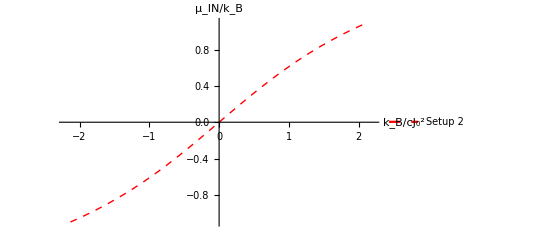

```mathematica
Plot[{Subscript[μI, s1N0]*10^2},{j,-2.2,2.2},PlotRange->{-1.1,1.1},PlotStyle->{{Red,Dashed,Thick},{Blue,Dashed,Thick},{Red,Dashed,Thick},{Green,Thick}},AxesLabel-> {Style["k_B/cJ_0^2",Bold,26],Style["μ_IN/k_B",Bold,22]},AxesStyle->Black,PlotLegends->Placed[{"Setup 2"},{Right,Bottom}],LabelStyle->{Bold,FontSize->19}]
```

spin config-1:  Δμ for charge current, (up_(e^-spin) * up_(impu spin))

```mathematica
xv=(k*T̄)/c j;
```

```mathematica
Subscript[μI, s1]=1/(6 (c j) DFI10)π (DFI120 (1-2 DTb) (k*T̄) π+√(48 (c j)^2 DFI10^2 DTb(k*T̄)+DFI120^2 (1-2 DTb)^2(k*T̄)^2 π^2));
Subscript[μI, s2]=1/(6 (c j) DFI20)π (DFI220 (1-2 DTb) (k*T̄) π+√(48 (c j)^2 DFI20^2 DTb(k*T̄)+DFI220^2 (1-2 DTb)^2(k*T̄)^2 π^2));
Subscript[μI, s3]=1/(6 (c j) DFI30)π (DFI320 (1-2 DTb) (k*T̄) π+√(48 (c j)^2 DFI30^2 DTb(k*T̄)+DFI320^2 (1-2 DTb)^2(k*T̄)^2 π^2));
Subscript[μI, s4]=1/(6 (c j) DFI40)π (DFI420 (1-2 DTb) (k*T̄) π+√(48 (c j)^2 DFI40^2 DTb(k*T̄)+DFI420^2 (1-2 DTb)^2(k*T̄)^2 π^2));
```

```mathematica
Subscript[μI, s10]=Subscript[μI, s1]/.{S-> 0.5,m->0.5,T1->4,T2->3};
Subscript[μI, s20]=Subscript[μI, s2]/.{S-> 0.5,m->-0.5,T1->4,T2->3};
Subscript[μI, s30]=Subscript[μI, s3]/.{S-> 0.5,m->0.5,T1->4,T2->3};
Subscript[μI, s40]=Subscript[μI, s4]/.{S-> 0.5,m->-0.5,T1->4,T2->3};
```

```mathematica
Subscript[μI, s1s]=1/(6 (c j) DFI10s)π (DFI120s (1-2 DTb) (k*T̄) π+√(48 (c j)^2 DFI10s^2 DTb(k*T̄)+DFI120s^2 (1-2 DTb)^2(k*T̄)^2 π^2));
Subscript[μI, s2s]=1/(6 (c j) DFI20s)π (DFI220s (1-2 DTb) (k*T̄) π+√(48 (c j)^2 DFI20s^2 DTb(k*T̄)+DFI220s^2 (1-2 DTb)^2(k*T̄)^2 π^2));
Subscript[μI, s3s]=1/(6 (c j) DFI30s)π (DFI320s (1-2 DTb) (k*T̄) π+√(48 (c j)^2 DFI30s^2 DTb(k*T̄)+DFI320s^2 (1-2 DTb)^2(k*T̄)^2 π^2));
Subscript[μI, s4s]=1/(6 (c j) DFI40s)π (DFI420s (1-2 DTb) (k*T̄) π+√(48 (c j)^2 DFI40s^2 DTb(k*T̄)+DFI420s^2 (1-2 DTb)^2(k*T̄)^2 π^2));
```

```mathematica
Subscript[μI, s1s0]=Subscript[μI, s1s]/.{S-> 0.5,m->0.5,T1->4,T2->3};
Subscript[μI, s2s0]=Subscript[μI, s2s]/.{S-> 0.5,m->-0.5,T1->4,T2->3};
Subscript[μI, s3s0]=Subscript[μI, s3s]/.{S-> 0.5,m->0.5,T1->4,T2->3};
Subscript[μI, s4s0]=Subscript[μI, s4s]/.{S-> 0.5,m->-0.5,T1->4,T2->3};
```

```mathematica
Subscript[μI, s20]/.{S-> 0.5,m->0.5,j-> 0.9}
```

0.00161257

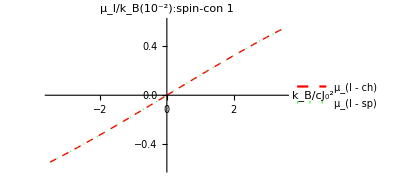
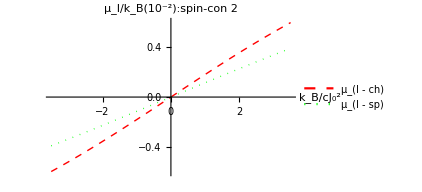

```mathematica
{Plot[{Subscript[μI, s10]*10^2,Subscript[μI, s1s0]*10^2},{j,-3.5,3.5},PlotRange->{-0.6,0.6},PlotStyle->{{Red,Dashed,Thick},{Green,Dotted,Thick},{Blue,Dashed,Thick},{Green,Thick}},AxesLabel-> {"k_B/cJ_0^2","μ_I/k_B(10^-2):spin-con 1"},AxesStyle->Black,PlotLegends->Placed[{"μ_(I - ch)","μ_(I - sp)"},{Right,Bottom}],LabelStyle->{Bold,FontSize->19}],Plot[{Subscript[μI, s20]*10^2,Subscript[μI, s3s0]*10^2},{j,-3.5,3.5},PlotRange->{-0.6,0.6},PlotStyle->{{Red,Dashed,Thick},{Green,Dotted,Thick},{Blue,Dotted,Thick},{Green,Thick}},AxesLabel-> {"k_B/cJ_0^2","μ_I/k_B(10^-2):spin-con 2"},AxesStyle->Black,PlotLegends->Placed[{"μ_(I - ch)","μ_(I - sp)"},{Right,Bottom}],LabelStyle->{Bold,FontSize->19}]}
```

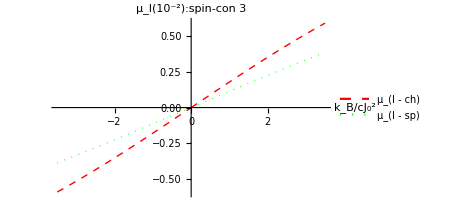
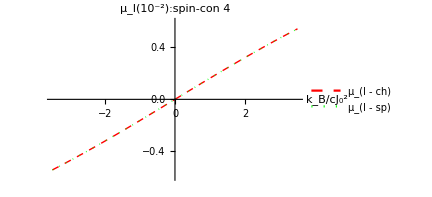

```mathematica
{Plot[{Subscript[μI, s30]*10^2,Subscript[μI, s3s0]*10^2},{j,-3.5,3.5},PlotRange->{-0.6,0.6},PlotStyle->{{Red,Dashed,Thick},{Green,Dotted,Thick},{Blue,Dotted,Thick},{Green,Thick}},AxesLabel-> {"k_B/cJ_0^2","μ_I(10^-2):spin-con 3"},AxesStyle->Black,PlotLegends->Placed[{"μ_(I - ch)","μ_(I - sp)"},{Right,Bottom}],LabelStyle->{Bold,FontSize->19}],Plot[{Subscript[μI, s40]*10^2,Subscript[μI, s4s0]*10^2},{j,-3.5,3.5},PlotRange->{-0.6,0.6},PlotStyle->{{Red,Dashed,Thick},{Green,Dotted,Thick},{Blue,Dashed,Thick},{Green,Thick}},AxesLabel-> {"k_B/cJ_0^2","μ_I(10^-2):spin-con 4"},AxesStyle->Black,PlotLegends->Placed[{"μ_(I - ch)","μ_(I - sp)"},{Right,Bottom}],LabelStyle->{Bold,FontSize->19}]}
```

## Δ_T noise

```mathematica
Ec=V (k*T̄)/c j;  
Ec1=V (k*T̄)/c j;
```

```mathematica
(*Define substitutions*)
sub1={V->Subscript[μI, s10]};
sub2={V->Subscript[μI, s20]};
sub3={V->Subscript[μI, s30]};
sub4={V->Subscript[μI, s40]};

sub1s={V->Subscript[μI, s1s0]};
sub2s={V->Subscript[μI, s2s0]};
sub3s={V->Subscript[μI, s3s0]};
sub4s={V->Subscript[μI, s4s0]};

subN={V->Subscript[μI, s1N0]};
```

```mathematica
{FshNv1,DFshNv1,DFsh2Nv1}={FshN,DFshN,DFshN2}/.subN;
{FthNv1,DFthNv1,DFth2Nv1}={FthN,DFthN,DFthN2}/.subN;
```

```mathematica
ScN=
4((-(FshN0+FshNv1)+xv(DFshN0+DFshNv1)(π^2/3)-xv^2*(π^2/6)*(DFshN20+DFsh2Nv1))* (ΔT/(2*T̄))+(xv*(π^2/3)(FshN0+FshNv1)-xv^2(DFshN20+DFsh2Nv1)*(π^2(7*π^2-15)/90))*(ΔT/(2*T̄))^2) ;
```

```mathematica
SsN=(ScN/.{m->0.5,T1->4,T2->3});
```

```mathematica
SthN=0.5(2(FthN0(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))*FthNv1)+4*xv^2*((1+(ΔT/2 T̄))*DFthN20+(1-(ΔT/2 T̄))*DFth2Nv1)(π^2/6)+(xv^2*(π^2/3)((1+(ΔT/2 T̄))*DFthN20-(1-(ΔT/2 T̄))*DFth2Nv1))(ΔT/2 T̄)+(xv^2*(π^2/6)((1+(ΔT/2 T̄))*DFthN20+(1-(ΔT/2 T̄))*DFth2Nv1))(ΔT/2 T̄)^2);
```

```mathematica
StN=(SthN/.{T1->4,T2->3});
```

## Charge Δ_T noise

Δμ spin-con 1 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)
{Fuushv1,DFuushv1,DFuush2v1}={Fuush,DFuush,DFuush2}/.sub1;
{Fudshv1,DFudshv1,DFudsh2v1}={Fudsh,DFudsh,DFudsh2}/.sub1;

{Fuuthv1,DFuuthv1,DFuuth2v1}={Fuuth,DFuuth,DFuuth2}/.sub1;
{Fudthv1,DFudthv1,DFudth2v1}={Fudth,DFudth,DFudth2}/.sub1;
```

```mathematica
Suuc1=
2((-(Fuush0+Fuushv1)+xv(DFuush0+DFuushv1)(π^2/3)-xv^2*(π^2/6)*(DFuush20+DFuush2v1))* (ΔT/(2*T̄))+(xv*(π^2/3)(Fuush0+Fuushv1)-xv^2(DFuush20+DFuush2v1)*(π^2(7*π^2-15)/90))*(ΔT/(2*T̄))^2) ;
(*Sudc1=
4k*T̄((-(Fudsh0+Fudshv1)+xv(DFudsh0+DFudshv1)(π^2/3)-xv^2*(π^2/6)*(DFudsh20+DFudsh2v1))* (ΔT/(2*T̄))+(xv*(π^2/3)(Fudsh0+Fudshv1)-xv^2(DFudsh20+DFudsh2v1)*(π^2(7*π^2-15)/90))*(ΔT/(2*T̄))^2);*)
```

```mathematica
Ssuu1=Suuc1/.{S->0.5,m->0.5,T1->4,T2->3 };
```

```mathematica
Suut1=(-(1/2)(2(Fuuth0(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))Fuuthv1)+4*xv^2*(DFuuth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFuuth2v1)(π^2/6)+(xv^2*(π^2/3)(DFuuth20(1+(ΔT/2 T̄))-(1-(ΔT/2 T̄))DFuuth2v1))(ΔT/2 T̄)+(xv^2*(π^2/6)(DFuuth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFuuth2v1))(ΔT/2 T̄)^2));
(*Sudt1=(-(2(k*T1*Fudth0+k*T2*Fudthv1)+2*xv^2*(k*T1*DFudth20+k*T2*DFudth2v1)(π^2/6)+(xv^2*(π^2/3)(k*T1*DFudth20-k*T2*DFudth2v1))(ΔT/2 T̄)+(xv^2*(π^2/6)(k*T1*DFudth20+k*T2*DFudth2v1))(ΔT/2 T̄)^2));*)
```

```mathematica
Stuu1=Suut1/.{S->0.5,m->0.5, T1->4,T2->3 };
```

Δμ spin-con 2 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)
{Fuushv2,DFuushv2,DFuush2v2}={Fuush,DFuush,DFuush2}/.sub2;
{Fudshv2,DFudshv2,DFudsh2v2}={Fudsh,DFudsh,DFudsh2}/.sub2;

{Fuuthv2,DFuuthv2,DFuuth2v2}={Fuuth,DFuuth,DFuuth2}/.sub2;
{Fudthv2,DFudthv2,DFudth2v2}={Fudth,DFudth,DFudth2}/.sub2;
```

```mathematica
Suuc2=
2((-(Fuush0+Fuushv2)+xv(DFuush0+DFuushv2)(π^2/3)-xv^2*(π^2/6)*(DFuush20+DFuush2v2))* (ΔT/(2*T̄))+(xv*(π^2/3)(Fuush0+Fuushv2)-xv^2(DFuush20+DFuush2v2)*(π^2(7*π^2-15)/90))*(ΔT/(2*T̄))^2) ;
Sudc2=
2((-(Fudsh0+Fudshv2)+xv(DFudsh0+DFudshv2)(π^2/3)-xv^2*(π^2/6)*(DFudsh20+DFudsh2v2))* (ΔT/(2*T̄))+(xv*(π^2/3)(Fudsh0+Fudshv2)-xv^2(DFudsh20+DFudsh2v2)*(π^2(7*π^2-15)/90))*(ΔT/(2*T̄))^2) ;
```

```mathematica
Suut2=(-(1/2)(2(Fuuth0(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))Fuuthv2)+4*xv^2*(DFuuth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFuuth2v2)(π^2/6)+(xv^2*(π^2/3)(DFuuth20(1+(ΔT/2 T̄))-(1-(ΔT/2 T̄))DFuuth2v2))(ΔT/2 T̄)+(xv^2*(π^2/6)(DFuuth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFuuth2v2))(ΔT/2 T̄)^2));
Sudt2=(-(1/2)(2(Fudth0(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))Fudthv2)+4*xv^2*(DFudth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFudth2v2)(π^2/6)+(xv^2*(π^2/3)(DFudth20(1+(ΔT/2 T̄))-(1-(ΔT/2 T̄))DFudth2v2))(ΔT/2 T̄)+(xv^2*(π^2/6)(DFudth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFudth2v2))(ΔT/2 T̄)^2));
```

```mathematica
Ssuu2=(Suuc2/.{S->0.5,m->-0.5,T1->4,T2->3 });
Ssud2=(Sudc2/.{S->0.5,m->-0.5, T1->4,T2->3 });
```

```mathematica
Stuu2=(Suut2/.{S->0.5,m->-0.5, T1->4,T2->3 });
Stud2=(Sudt2/.{S->0.5,m->-0.5, T1->4,T2->3 });
```

Δμ spin-con 3 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)

{Fddshv3,DFddshv3,DFddsh2v3}={Fddsh,DFddsh,DFddsh2}/.sub3;
{Fdushv3,DFdushv3,DFdush2v3}={Fdush,DFdush,DFdush2}/.sub3;

{Fddthv3,DFddthv3,DFddth2v3}={Fddth,DFddth,DFddth2}/.sub3;
{Fduthv3,DFduthv3,DFduth2v3}={Fduth,DFduth,DFduth2}/.sub3;
```

```mathematica
Subscript[μI, s3]/.{S->0.5,m->-0.5,T1-> 4,T2-> 3}
```

(0.498856 (-0.34651+√(0.120069+0.00227832 j^2)))/j

```mathematica
Sddc3=
2((-(Fddsh0+Fddshv3)+xv(DFddsh0+DFddshv3)(π^2/3)-xv^2*(π^2/6)*(DFddsh20+DFddsh2v3))* (ΔT/(2*T̄))+(xv*(π^2/3)(Fddsh0+Fddshv3)-xv^2(DFddsh20+DFddsh2v3)*(π^2(7*π^2-15)/90))*(ΔT/(2*T̄))^2) ;
Sduc3=
2((-(Fdush0+Fdushv3)+xv(DFdush0+DFdushv3)(π^2/3)-xv^2*(π^2/6)*(DFdush20+DFdush2v3))* (ΔT/(2*T̄))+(xv*(π^2/3)(Fdush0+Fdushv3)-xv^2(DFdush20+DFdush2v3)*(π^2(7*π^2-15)/90))*(ΔT/(2*T̄))^2) ;
```

```mathematica
Sddt3=(-(1/2)(2(Fddth0(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))Fddthv3)+4*xv^2*(DFddth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFddth2v3)(π^2/6)+(xv^2*(π^2/3)(DFddth20(1+(ΔT/2 T̄))-(1-(ΔT/2 T̄))DFddth2v3))(ΔT/2 T̄)+(xv^2*(π^2/6)(DFddth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFddth2v3))(ΔT/2 T̄)^2));
Sdut3=(-(1/2)(2(Fduth0(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))Fduthv3)+4*xv^2*(DFduth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFduth2v3)(π^2/6)+(xv^2*(π^2/3)(DFduth20(1+(ΔT/2 T̄))-(1-(ΔT/2 T̄))DFduth2v3))(ΔT/2 T̄)+(xv^2*(π^2/6)(DFduth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFduth2v3))(ΔT/2 T̄)^2));
```

```mathematica
Ssdd3=(Sddc3/.{S->0.5,m->0.5,T1->4,T2->3 });
Ssdu3=(Sduc3/.{S->0.5,m->0.5, T1->4,T2->3 });
```

```mathematica
Stdd3=(Sddt3/.{S->0.5,m->0.5, T1->4,T2->3 });
Stdu3=(Sdut3/.{S->0.5,m->0.5, T1->4,T2->3 });
```

Δμ spin-con 4 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)

{Fddshv4,DFddshv4,DFddsh2v4}={Fddsh,DFddsh,DFddsh2}/.sub4;
{Fdushv4,DFdushv4,DFdush2v4}={Fdush,DFdush,DFdush2}/.sub4;

{Fddthv4,DFddthv4,DFddth2v4}={Fddth,DFddth,DFddth2}/.sub4;
{Fduthv4,DFduthv4,DFduth2v4}={Fduth,DFduth,DFduth2}/.sub4;
```

```mathematica
Sddc4=
2((-(Fddsh0+Fddshv4)+xv(DFddsh0+DFddshv4)(π^2/3)-xv^2*(π^2/6)*(DFddsh20+DFddsh2v4))* (ΔT/(2*T̄))+(xv*(π^2/3)(Fddsh0+Fddshv4)-xv^2(DFddsh20+DFddsh2v4)*(π^2(7*π^2-15)/90))*(ΔT/(2*T̄))^2) ;
```

```mathematica
Sddt4=(-(1/2)(2(Fddth0(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))*Fddthv4)+4*xv^2*(DFddth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFddth2v4)(π^2/6)+(xv^2*(π^2/3)(DFddth20(1+(ΔT/2 T̄))-(1-(ΔT/2 T̄))*DFddth2v4))(ΔT/2 T̄)+(xv^2*(π^2/6)(DFddth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))*DFddth2v4))(ΔT/2 T̄)^2));
```

```mathematica
Ssdd4=(Sddc4/.{S->0.5,m->-0.5,T1->4,T2->3 });
Stdd4=(Sddt4/.{S->0.5,m->-0.5, T1->4,T2->3 });
```

Charge Δ_T noise : Δμ spin-con ( for spin  flip Δ_T noise)

```mathematica
Duush=(Ssuu1+Ssuu2);
Dudsh=(Ssud2);
Dddsh=(Ssdd3+Ssdd4);
Ddush=(Ssdu3);
Dlcuush=(Duush+Dudsh+Dddsh+Ddush);
```

```mathematica
Duuth=(Stuu1+Stuu2);
Dudth=(Stud2);
Dddth=(Stdd3+Stdd4);
Dduth=(Stdu3);
Dlcuuth=(Duuth+Dudth+Dddth+Dduth);
```

## Spin Δ_T noise

Δμ spin-con 1 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)
{Fuushv1s,DFuushv1s,DFuush2v1s}={Fuush,DFuush,DFuush2}/.sub1s;
{Fudshv1s,DFudshv1s,DFudsh2v1s}={Fudsh,DFudsh,DFudsh2}/.sub1s;

{Fuuthv1s,DFuuthv1s,DFuuth2v1s}={Fuuth,DFuuth,DFuuth2}/.sub1s;
{Fudthv1s,DFudthv1s,DFudth2v1s}={Fudth,DFudth,DFudth2}/.sub1s;
```

```mathematica
Suuc1s=
4((-(Fuush0+Fuushv1s)+xv(DFuush0+DFuushv1s)(π^2/3)-xv^2*(π^2/6)*(DFuush20+DFuush2v1s))* (ΔT/(2*T̄))+(xv*(π^2/3)(Fuush0+Fuushv1s)-xv^2(DFuush20+DFuush2v1s)*(π^2(7*π^2-15)/90))*(ΔT/(2*T̄))^2) ;
```

```mathematica
Ssuu1s=(Suuc1s/.{S->0.5,m->0.5,T1->4,T2->3});
```

```mathematica
Suut1s=(-(1/2)(2(Fuuth0(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))Fuuthv1s)+2*xv^2*(DFuuth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFuuth2v1s)(π^2/6)+(xv^2*(π^2/3)(DFuuth20(1+(ΔT/2 T̄))-(1-(ΔT/2 T̄))DFuuth2v1s))(ΔT/2 T̄)+(xv^2*(π^2/6)(DFuuth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFuuth2v1s))(ΔT/2 T̄)^2));
```

```mathematica
Stuu1s=(Suut1s/.{S->0.5,m->0.5, T1->4,T2->3});
```

Δμ spin-con 2 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)
{Fuushv2s,DFuushv2s,DFuush2v2s}={Fuush,DFuush,DFuush2}/.sub3s;
{Fudshv2s,DFudshv2s,DFudsh2v2s}={Fudsh,DFudsh,DFudsh2}/.sub3s;

{Fuuthv2s,DFuuthv2s,DFuuth2v2s}={Fuuth,DFuuth,DFuuth2}/.sub3s;
{Fudthv2s,DFudthv2s,DFudth2v2s}={Fudth,DFudth,DFudth2}/.sub3s;
```

```mathematica
Suuc2s=
4((-(Fuush0+Fuushv2s)+xv(DFuush0+DFuushv2s)(π^2/3)-xv^2*(π^2/6)*(DFuush20+DFuush2v2s))* (ΔT/(2*T̄))+(xv*(π^2/3)(Fuush0+Fuushv2s)-xv^2(DFuush20+DFuush2v2s)*(π^2(7*π^2-15)/90))*(ΔT/(2*T̄))^2) ;
Sudc2s=
4((-(Fudsh0+Fudshv2s)+xv(DFudsh0+DFudshv2s)(π^2/3)-xv^2*(π^2/6)*(DFudsh20+DFudsh2v2s))* (ΔT/(2*T̄))+(xv*(π^2/3)(Fudsh0+Fudshv2s)-xv^2(DFudsh20+DFudsh2v2s)*(π^2(7*π^2-15)/90))*(ΔT/(2*T̄))^2) ;
```

```mathematica
Suut2s=(-(1/2)(2(Fuuth0(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))Fuuthv2s)+2*xv^2*(DFuuth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFuuth2v2s)(π^2/6)+(xv^2*(π^2/3)(DFuuth20(1+(ΔT/2 T̄))-(1-(ΔT/2 T̄))DFuuth2v2s))(ΔT/2 T̄)+(xv^2*(π^2/6)(DFuuth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFuuth2v2s))(ΔT/2 T̄)^2));
Sudt2s=(-(1/2)(2(Fudth0(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))Fudthv2s)+2*xv^2*(k*T1*DFudth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFudth2v2s)(π^2/6)+(xv^2*(π^2/3)(DFudth20(1+(ΔT/2 T̄))-(1-(ΔT/2 T̄))DFudth2v2s))(ΔT/2 T̄)+(xv^2*(π^2/6)(DFudth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFudth2v2s))(ΔT/2 T̄)^2));
```

```mathematica
Ssuu2s=(Suuc2s/.{S->0.5,m->-0.5,T1->4,T2->3 });
Ssud2s=(Sudc2s/.{S->0.5,m->-0.5, T1->4,T2->3 });
```

```mathematica
Stuu2s=(Suut2s/.{S->0.5,m->-0.5, T1->4,T2->3 });
Stud2s=(Sudt2s/.{S->0.5,m->-0.5, T1->4,T2->3 });
```

Δμ spin-con 3 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)
{Fddshv3s,DFddshv3s,DFddsh2v3s}={Fddsh,DFddsh,DFddsh2}/.sub3s;
{Fdushv3s,DFdushv3s,DFdush2v3s}={Fdush,DFdush,DFdush2}/.sub3s;

{Fddthv3s,DFddthv3s,DFddth2v3s}={Fddth,DFddth,DFddth2}/.sub3s;
{Fduthv3s,DFduthv3s,DFduth2v3s}={Fduth,DFduth,DFduth2}/.sub3s;
```

```mathematica
Sddc3s=
4((-(Fddsh0+Fddshv3s)+xv(DFddsh0+DFddshv3s)(π^2/3)-xv^2*(π^2/6)*(DFddsh20+DFddsh2v3s))* (ΔT/(2*T̄))+(xv*(π^2/3)(Fddsh0+Fddshv3s)-xv^2(DFddsh20+DFddsh2v3s)*(π^2(7*π^2-15)/90))*(ΔT/(2*T̄))^2) ;
Sduc3s=
4((-(Fdush0+Fdushv3s)+xv(DFdush0+DFdushv3s)(π^2/3)-xv^2*(π^2/6)*(DFdush20+DFdush2v3s))* (ΔT/(2*T̄))+(xv*(π^2/3)(Fdush0+Fdushv3s)-xv^2(DFdush20+DFdush2v3s)*(π^2(7*π^2-15)/90))*(ΔT/(2*T̄))^2) ;
```

```mathematica
Sddt3s=(-(1/2)(2(Fddth0(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))Fddthv3s)+2*xv^2*(DFddth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFddth2v3s)(π^2/6)+(xv^2*(π^2/3)(DFddth20(1+(ΔT/2 T̄))-(1-(ΔT/2 T̄))DFddth2v3s))(ΔT/2 T̄)+(xv^2*(π^2/6)(DFddth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFddth2v3s))(ΔT/2 T̄)^2));
Sdut3s=(-(1/2)(2(Fduth0(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))Fduthv3s)+2*xv^2*(DFduth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFduth2v3s)(π^2/6)+(xv^2*(π^2/3)(DFduth20(1+(ΔT/2 T̄))-(1-(ΔT/2 T̄))DFduth2v3s))(ΔT/2 T̄)+(xv^2*(π^2/6)(DFduth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFduth2v3s))(ΔT/2 T̄)^2));
```

```mathematica
Ssdd3s=(Sddc3s/.{S->0.5,m->0.5,T1->4,T2->3 });
Ssdu3s=(Sduc3s/.{S->0.5,m->0.5, T1->4,T2->3 });
```

```mathematica
Stdd3s=(Sddt3s/.{S->0.5,m->0.5, T1->4,T2->3 });
Stdu3s=(Sdut3s/.{S->0.5,m->0.5, T1->4,T2->3 });
```

Δμ spin-con 4 ( for spin  flip Δ_T noise)

```mathematica
(*Compute values*)
{Fddshv4s,DFddshv4s,DFddsh2v4s}={Fddsh,DFddsh,DFddsh2}/.sub4s;
{Fdushv4s,DFdushv4s,DFdush2v4s}={Fdush,DFdush,DFdush2}/.sub4s;

{Fddthv4s,DFddthv4s,DFddth2v4s}={Fddth,DFddth,DFddth2}/.sub4s;
{Fduthv4s,DFduthv4s,DFduth2v4s}={Fduth,DFduth,DFduth2}/.sub4s;
```

```mathematica
Sddc4s=
4((-(Fddsh0+Fddshv4s)+xv(DFddsh0+DFddshv4s)(π^2/3)-xv^2*(π^2/6)*(DFddsh20+DFddsh2v4s))* (ΔT/(2*T̄))+(xv*(π^2/3)(Fddsh0+Fddshv4s)-xv^2(DFddsh20+DFddsh2v4s)*(π^2(7*π^2-15)/90))*(ΔT/(2*T̄))^2) ;
```

```mathematica
Sddt4s=(-(1/2)(2(Fddth0(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))Fddthv4s)+2*xv^2*(DFddth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFddth2v4s)(π^2/6)+(xv^2*(π^2/3)(DFddth20(1+(ΔT/2 T̄))-(1-(ΔT/2 T̄))DFddth2v4s))(ΔT/2 T̄)+(xv^2*(π^2/6)(DFddth20(1+(ΔT/2 T̄))+(1-(ΔT/2 T̄))DFddth2v4s))(ΔT/2 T̄)^2));
```

```mathematica
Ssdd4s=(Sddc4s/.{S->0.5,m->0.5,T1->4,T2->3});
```

```mathematica
Stdd4s=(Sddt4s/.{S->0.5,m->0.5, T1->4,T2->3});
```

Spin Δ_T noise

```mathematica
Duushs=(Ssuu1s+Ssuu2s);
Dudshs=(Ssud2s);
Dddshs=(Ssdd3s+Ssdd4s);
Ddushs=(Ssdu3s);
Dlcuushs=(Duushs+Dddshs-Ddushs-Dudshs);
```

```mathematica
Duuths=(Stuu1s+Stuu2s);
Dudths=(Stud2s);
Dddths=(Stdd3s+Stdd4s);
Dduths=(Stdu3s);
Dlcuuths=Duuths-Dudths+Dddths-Dduths;
```

In the approximation limit (k_B T̄/cJ_0^2) << 1

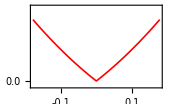

```mathematica
Plot2=Plot[{(SsN +StN)},{j,-.19,0.19},PlotRange->{-0.01,.14},Frame->True,FrameStyle->Thickness[0.002],Axes->False,PlotStyle->{{Red,Thickness[0.007]}},FrameTicksStyle->Directive[Black,10,Bold],FrameTicks->{{{{0,"0.0"},{0.1,"0.1"},{0.5,"0.5"}},None},{{{-0.1,"-0.1"},{0,"0.0"},{0.1,"0.1"}},None}},FrameLabel-> {Style["k_BT̄/cJ_0^2",8,Black,Bold],Style["Δ_T^N",8,Black,Bold]},LabelStyle->Directive[Bold,Large]]
```

```mathematica
Plot of Subscript[Δ, T]^η noise in unit of (2 e^2(Subscript[k, B] T̄))/h for setup 2 given in Fig. 6(a)
```

```mathematica
Plot[{(Dlcuush+Dlcuuth),(Dlcuushs+Dlcuuths),(SsN +StN)},{j,-.19,.19},PlotRange->{-5,5.3},Frame->True,FrameStyle->Thickness[0.0046],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.0075]},{Blue,Dashed,Thickness[0.0075]},{Red,Thickness[0.0065]},{Magenta,Dashed,Thickness[0.0075]}},FrameTicksStyle->Directive[Black,17,Bold],FrameTicks->{{{{-10,"-10.0"},{-5,"-5.0"},{0,"0.0"},{5,"5.0"},{10,"10.0"}},None},{{{-2,"-2.0"},{-0.1,"-0.1"},{0,"0.0"},{0.1,"0.1"},{2,"2.0"}},None}},FrameLabel-> {Style["k_BT̄/cJ_0^2",19,Black,Bold],Style["Δ_T^η(2e^2(k_BT̄)/h)",18,Black,Bold]},LabelStyle->Directive[Bold,Large]]
```

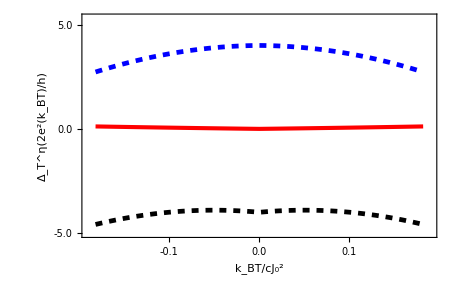

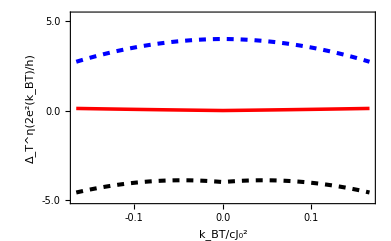

```mathematica
Plot[{(Dlcuush+Dlcuuth),(Dlcuushs+Dlcuuths),(SsN +StN)},{j,-.19,.19},PlotRange->{-5,5.3},Frame->True,FrameStyle->Thickness[0.0046],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.0075]},{Blue,Dashed,Thickness[0.0075]},{Red,Thickness[0.0065]},{Magenta,Dashed,Thickness[0.0075]}},FrameTicksStyle->Directive[Black,17,Bold],FrameTicks->{{{{-10,"-10.0"},{-5,"-5.0"},{0,"0.0"},{5,"5.0"},{10,"10.0"}},None},{{{-2,"-2.0"},{-0.1,"-0.1"},{0,"0.0"},{0.1,"0.1"},{2,"2.0"}},None}},FrameLabel-> {Style["k_BT̄/cJ_0^2",19,Black,Bold],Style["Δ_T^η(2e^2(k_BT̄)/h)",18,Black,Bold]},LabelStyle->Directive[Bold,Large]]
```

```mathematica
Plot of Subscript[Δ, Tsh(th)]^η noise in unit of (2 e^2(Subscript[k, B] T̄))/h for setup 2 given in Fig. 9(b)
```

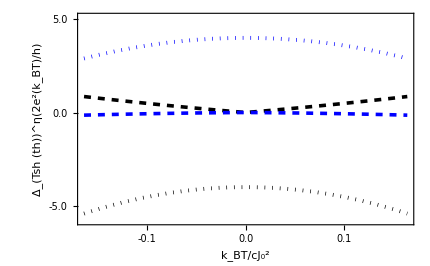

```mathematica
Plot[{Dlcuush,Dlcuuth,Dlcuushs ,Dlcuuths},{j,-0.19,0.19},PlotRange->{-5.8,5.1},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.006]},{Black,Dotted,Thickness[0.0065]},{Blue,Dashed,Thickness[0.006]},{Blue,Dotted,Thickness[0.0065]},{Red,Dashed,Thickness[0.007]},{Red,Dotted,Thickness[0.0075]}},FrameTicksStyle->Directive[Black,17,Bold],FrameTicks->{{{{-10,"-10.0"},{-5,"-5.0"},{0,"0.0"},{5,"5.0"}},None},{{{-2,"-2.0"},{-0.5,"-0.1"},{0,"0.0"},{0.5,"0.1"}},None}},FrameLabel-> {Style["k_BT̄/cJ_0^2",19,Black,Bold],Style["Δ_(Tsh (th))^η(2e^2(k_BT̄)/h)",18,Black,Bold]},LabelStyle->Directive[Bold,Large]]
```

## Ratio Δ_Tsh^η/Δ_Tth^η

```mathematica
Rch=Abs[Dlcuush /Dlcuuth]//Simplify;
```

```mathematica
RN=(SsN)/(StN);
```

```mathematica
Rsp=Abs[(Dlcuushs)/Dlcuuths];
```

```mathematica
Plot of ratio |Subscript[Δ, Tsh]^η/Subscript[Δ, Tth]^η| noise  for setup 2 given in Fig. 6(b)
```

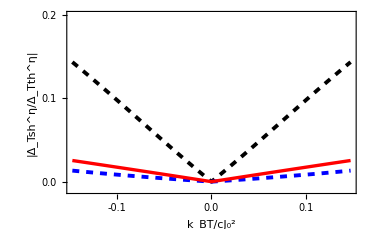

```mathematica
Plot[{Rch,Rsp,RN},{j,-.18,.18},PlotRange->{-0.01,0.2},Frame->True,FrameStyle->Thickness[0.0046],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.0075]},{Blue,Dashed,Thickness[0.0075]},{Red,Thickness[0.0065]},{Magenta,Dashed,Thickness[0.0075]}},FrameTicksStyle->Directive[Black,17,Bold],FrameTicks->{{{{-2,"-2.0"},{-4,"-4.0"},{0,"0.0"},{0.2,"0.2"},{0.1,"0.1"}},None},{{{-0.1,"-0.1"},{0,"0.0"},{0.1,"0.1"}},None}},FrameLabel-> {Style["k_BT̄/cJ_0^2",19,Black,Bold],Style["|Δ_Tsh^η/Δ_Tth^η|",18,Black,Bold]},LabelStyle->Directive[Bold,Large]]
```